```mathematica
Unprotect[Power];
(*Power[b_?Negative,e_]:=(-b)^e;*)
Power[0.,e_]:=0.;
Power[0,e_]:=0;
Power[0,0]:=1;
Power[0.,0]:=1;
Protect[Power];

Needs["CCompilerDriver`"];
SetSystemOptions["CompileOptions"->"CompileReportExternal"->True];
Off[General::stop];

Compiler`$CCompilerOptions={
(*"ShellCommandFunction"->Print,
"ShellOutputFunction"->Print,*)
(*"Compiler"->CCompilerDriver`GCCCompiler`GCCCompiler,*)
"SystemCompileOptions"->{"-O3"}
};

getTickers = Block[{tickers},
tickers = FinancialData["NYSE", "Members"];
Print[StringForm["`` tickers found.",Length[tickers]]];
tickers
]&;
SetAttributes[getTickers, HoldAll];

interpolateTickerData= Block[{
i,
z,
mint=Min[#[[All,1]]],
dat=({
(*0,0,0,0,0,0,0,0,
0,0,0,0,0,0,*)
(*#[[3]],*)
(#[[1]]-mint)/86400,
#[[2]]
}&)/@#
},
(*For[z=1,z≤14,++z,
For[i=Length[dat],i ≥ z+1, --i,
dat[[i,z]]=(
100000000*((dat[[i,-2]]/dat[[i-z,-2]]) - 1)
/
(dat[[i,-1]]-dat[[i-z,-1]]) 
);
];
];*)
dat
]&;
SetAttributes[interpolateTickerData, HoldAll];

interpolateTickersData = Module[{idx=0,ticker=""},Block[{idata},
SetSharedVariable[idx,ticker];
PrintTemporary[Framed[Style[
StringForm["\nInterpolating Tickers Data...\n`` ``/`` ``", ProgressIndicator[Dynamic[idx/Length[#]]], Dynamic[idx],Length[#], Dynamic[ticker]
],{FontFamily->"Verdana",FontSize->11,FontColor->RGBColor[0.2,0.4,0.6]}
],{FrameMargins->{{24,24},{8,8}},FrameStyle->RGBColor[0.2,0.4,0.6],Background->RGBColor[0.96,0.98,1.]}
]];
idata = Map[
(tdata=interpolateTickerData[#[[2]]];ticker = #[[1]];++idx;{#[[1]],tdata})&
,#];
Print[StringForm["`` ticker datas were successfully interpolated.", Length[idata]]];
idata
]]&;
SetAttributes[interpolateTickersData, HoldAll];

getTickerData = Block[{data=Quiet[FinancialData[#,"OHLCV",#2]]}, 
If[MatchQ[data,_List],
{#,
{AbsoluteTime[#[[1]]],#[[2,4]],#[[2,5]]}&/@ data
}]
]&;
SetAttributes[getTickerData, HoldAll];

getTickersData = Module[{idx=0,ticker=""},Block[{tdata,tickersData,timespec=#2},
	SetSharedVariable[idx,ticker];
	PrintTemporary[Framed[Style[
StringForm["\nFetching Tickers Data...\n`` ``/`` ``", ProgressIndicator[Dynamic[idx/Length[#]]], Dynamic[idx],Length[#], Dynamic[ticker]
],{FontFamily->"Verdana",FontSize->11,FontColor->RGBColor[0.2,0.4,0.6]}
],{FrameMargins->{{24,24},{8,8}},FrameStyle->RGBColor[0.2,0.4,0.6],Background->RGBColor[0.96,0.98,1.]}
]];
	tickersData=
DeleteCases[
Map[
(tdata=getTickerData[#,timespec];ticker = #;++idx;tdata)&
,#] 
,Null];
Print[StringForm["`` out of `` ticker datas were valid and successfully fetched.", Length[tickersData],Length[#]]];
tickersData
]]&;
SetAttributes[getTickersData, HoldAll];

mutationValM=  Compile[{},
N[RandomInteger[{-16777215,16777215}]*2^(RandomInteger[{-126,127}])],{{RandomInteger[_],_Integer},{N[_],_Real}},CompilationTarget->"C",
CompilationOptions->{
"InlineExternalDefinitions"->True,
"ExpressionOptimization"->True,
"InlineCompiledFunctions"->True
},RuntimeOptions->{
"CatchMachineOverflow" ->False,
"CatchMachineUnderflow"->False,
"CatchMachineIntegerOverflow" ->False,
"CompareWithTolerance" ->False,
"EvaluateSymbolically"->False,
"RuntimeErrorHandler"->Evaluate,
"WarningMessages"->True
}];

mutationValE=  Compile[{},
RandomInteger[{-126,127}]
,{{RandomInteger[_],_Integer}},CompilationTarget->"C",
CompilationOptions->{
"InlineExternalDefinitions"->True,
"ExpressionOptimization"->True,
"InlineCompiledFunctions"->True
},RuntimeOptions->{
"CatchMachineOverflow" ->False,
"CatchMachineUnderflow"->False,
"CatchMachineIntegerOverflow" ->False,
"CompareWithTolerance" ->False,
"EvaluateSymbolically"->False,
"RuntimeErrorHandler"->Evaluate,
"WarningMessages"->True
}];

fitness= Compile[{{tickerData,_Real,2},{speciesParms,_Real,1}},Block[{isholding = 0.,spent =0.,sold = 0.},
Scan[
((*If[#[[1]]==0.,Return[]];*)
If[(
      speciesParms[[1*2]]*#[[1]]^speciesParms[[1*2+1]]
+speciesParms[[2*2]]*#[[2]]^speciesParms[[2*2+1]]
+speciesParms[[3*2]]*#[[3]]^speciesParms[[3*2+1]]
+speciesParms[[4*2]]*#[[4]]^speciesParms[[4*2+1]]
+speciesParms[[5*2]]*#[[5]]^speciesParms[[5*2+1]]
+speciesParms[[6*2]]*#[[6]]^speciesParms[[6*2+1]]
)<=speciesParms[[1]],
If[isholding ==0.,
spent+=(isholding=#[[7]]);
];,
 If[isholding≠0.,
sold += #[[7]];
isholding = 0.;
];
];)&,tickerData];
If[spent >isholding, sold/(spent-isholding), 1.]
],{{isholding,_Real},{spent,_Real},{sold,_Real}},CompilationTarget->"C",CompilationOptions->{
"InlineExternalDefinitions"->True,
"ExpressionOptimization"->True,
"InlineCompiledFunctions"->True
},RuntimeOptions->{
"CatchMachineOverflow" ->False,
"CatchMachineUnderflow"->False,
"CatchMachineIntegerOverflow" ->False,
"CompareWithTolerance" ->False,
"EvaluateSymbolically"->False,
"RuntimeErrorHandler"->Evaluate,
"WarningMessages"->True
},RuntimeAttributes->Listable,Parallelization->True];
SetAttributes[fitness,HoldAll];

fitnessStats[tickerData_,speciesParms_]:=Block[{isholding = 0.,spent =0.,sold = 0.,buygraph={},sellgraph={}},
Scan[
((*If[#[[1]]==0.,Return[]];*)
If[(
      speciesParms[[1*2]]*#[[1]]^speciesParms[[1*2+1]]
+speciesParms[[2*2]]*#[[2]]^speciesParms[[2*2+1]]
+speciesParms[[3*2]]*#[[3]]^speciesParms[[3*2+1]]
+speciesParms[[4*2]]*#[[4]]^speciesParms[[4*2+1]]
+speciesParms[[5*2]]*#[[5]]^speciesParms[[5*2+1]]
+speciesParms[[6*2]]*#[[6]]^speciesParms[[6*2+1]]
)<=speciesParms[[1]],
If[isholding ==0.,
spent+=(isholding=#[[7]]);
AppendTo[buygraph,{#[[8]],#[[7]]}];
];,
 If[isholding≠0.,
sold += #[[7]];
isholding = 0.;
AppendTo[sellgraph,{#[[8]],#[[7]]}];
];
];)&,tickerData];
{"fitness"->If[spent >isholding, sold/(spent-isholding), 1.],
"buygraph"->buygraph,
"sellgraph"->sellgraph
}];
SetAttributes[fitnessStats,HoldAll];

Needs["OpenCLLink`"];
clFitness = OpenCLFunctionLoad["
__kernel void fitness(__global float* tickersData, __global float* out, uint count,
float magicConstant,
float multiplier1, int exponent1,
float multiplier2, int exponent2,
float multiplier3, int exponent3,
float multiplier4, int exponent4,
float multiplier5, int exponent5,
float multiplier6, int exponent6
) {

    uint gid = get_global_id(0);
	float spent = 0., sold = 0., isHolding = 0.;

	for (uint i = gid * count; i < count; i += 8){
		if (  multiplier1  *  pown((double)tickersData[i+0],  exponent1)
			+ multiplier2  *  pown((double)tickersData[i+1],  exponent2)
			+ multiplier3  *  pown((double)tickersData[i+2],  exponent3)
			+ multiplier4  *  pown((double)tickersData[i+3],  exponent4)
			+ multiplier5  *  pown((double)tickersData[i+4],  exponent5)
			+ multiplier6  *  pown((double)tickersData[i+5],  exponent6)
		    <= magicConstant){
			if (!isHolding){
				spent += (isHolding = tickersData[i+6]);
			}
		}else if (isHolding){
			sold += tickersData[i+6];
			isHolding = 0.;
		}
    }
	out[gid] = (spent > isHolding) ? sold / (spent - isHolding) : 1.;
}", "fitness", {
{"Float", 1,"Input"}, {"Float",1,"Output"} ,"UnsignedInteger32",
"Float",
"Float","Integer32",
"Float","Integer32",
"Float","Integer32",
"Float","Integer32",
"Float","Integer32",
"Float","Integer32"
}, 1,CompileOptions->{
"-cl-strict-aliasing"
}
,ShellCommandFunction->Print
,ShellOutputFunction->Print
];
SetAttributes[clFitness,HoldAll];
clBootstrap =(
clTickersData=OpenCLMemoryLoad[Flatten[#],"Float"];
clFitnessOut=OpenCLMemoryAllocate["Float",Length[#]];
OpenCLMemoryCopyToDevice[clTickersData];
OpenCLMemoryCopyToDevice[clFitnessOut];
clTickerCount=Length[#];
clDataCount=Length[#[[1]]]*Length[#[[1,1]]];
)&;
SetAttributes[clBootstrap,HoldAll];
clFitnessEx=(
OpenCLMemoryGet[clFitness[clTickersData,clFitnessOut,clDataCount,
mutatedParms[[1]],
mutatedParms[[2]],
mutatedParms[[3]],
mutatedParms[[4]],
mutatedParms[[5]],
mutatedParms[[6]],
mutatedParms[[7]],
mutatedParms[[8]],
mutatedParms[[9]],
mutatedParms[[10]],
mutatedParms[[11]],
mutatedParms[[12]],
mutatedParms[[13]],
clTickerCount][[1]]]
)&;
SetAttributes[clFitnessEx,HoldAll];


main =Compile[{{tickersData,_Real,3}},Block[{
 mutationIdx,
parmsRange=Range[Length[curParms]],
parmsRangeRev=Range[Length[curParms],1,-1]
},
mutatedFitness=curFitness=Mean[fitness[tickersData,mutatedParms=curParms]];
While[True,
mutationIdx=RandomSample[parmsRange,
RandomChoice[parmsRangeRev->parmsRange]
];
mutatedParms[[mutationIdx]]=
If[EvenQ[#],mutationValE[],mutationValM[]]&/@mutationIdx;
If[(mutatedFitness=Mean[fitness[tickersData,mutatedParms]])≥curFitness
,curFitness= mutatedFitness; 
curParms[[mutationIdx]]=mutatedParms[[mutationIdx]];
,mutatedParms[[mutationIdx]]=curParms[[mutationIdx]];
];
++rounds;
];
];,{{parmsRange,_Integer,1},{parmsRangeRev,_Integer,1},{rounds,_Integer},{curFitness,_Real},{mutatedFitness,_Real},{mutationIdx,_Integer,1},{mutatedParms,_Real,1},{curParms,_Real,1},{fitness[_,_],_Real,1},{mutationValM[],_Real},{mutationValE[],_Real},{Mean[_],_Real},{Length[_],_Integer},{RandomInteger[_],_Integer},{RandomSample[_,_],_Integer,1},{Range[__],_Integer,1},{RandomChoice[_],_Integer},{Table[_,_],_Real,1}},CompilationTarget->"C",CompilationOptions->{
"InlineExternalDefinitions"->False,
"ExpressionOptimization"->True,
"InlineCompiledFunctions"->True
},
RuntimeOptions->{
"CatchMachineOverflow" ->False,
"CatchMachineUnderflow"->False,
"CatchMachineIntegerOverflow" ->False,
"CompareWithTolerance" ->False,
"EvaluateSymbolically"->False,
"RuntimeErrorHandler"->Evaluate,
"WarningMessages"->True
}];

clMain =Compile[{{x,_Integer}},Block[{
 mutationIdx,
parmsRange=Range[Length[curParms]],
parmsRangeRev=Range[Length[curParms],1,-1]
},
mutatedParms=curParms;
mutatedFitness=curFitness=Mean[clFitnessEx[]];
While[True,
mutationIdx=RandomSample[parmsRange,
RandomChoice[parmsRangeRev->parmsRange]
];
mutatedParms[[mutationIdx]]=
If[EvenQ[#],mutationValE[],mutationValM[]]&/@mutationIdx;
If[(mutatedFitness=Mean[clFitnessEx[]])≥curFitness
,curFitness= mutatedFitness; 
curParms[[mutationIdx]]=mutatedParms[[mutationIdx]];
,mutatedParms[[mutationIdx]]=curParms[[mutationIdx]];
];
++rounds;
];
];,{{clFitnessEx[],_Real,1},{parmsRange,_Integer,1},{parmsRangeRev,_Integer,1},{rounds,_Integer},{curFitness,_Real},{mutatedFitness,_Real},{mutationIdx,_Integer,1},{mutationValM[],_Real},{mutationValE[],_Integer},{Mean[_],_Real},{Length[_],_Integer},{RandomSample[_,_],_Integer,1},{Range[__],_Integer,1},{RandomChoice[_],_Integer},{Table[_,_],_Real,1}},CompilationTarget->"C",CompilationOptions->{
"InlineExternalDefinitions"->False,
"ExpressionOptimization"->True,
"InlineCompiledFunctions"->True
},
RuntimeOptions->{
"CatchMachineOverflow" ->False,
"CatchMachineUnderflow"->False,
"CatchMachineIntegerOverflow" ->False,
"CompareWithTolerance" ->False,
"EvaluateSymbolically"->False,
"RuntimeErrorHandler"->Evaluate,
"WarningMessages"->True
}];
```

-cl-strict-aliasing -DUSING_OPENCL_FUNCTION=1 -DOPENCLLINK_USING_INTEL -Dmint=long -DReal_t=double -DUSING_DOUBLE_PRECISIONQ=1

Compile::extscalar: Length[curParms] cannot be compiled and will be evaluated externally. The result is assumed to be of type Integer.

Compile::exttensor: fitness[tickersData, mutatedParms = curParms] cannot be compiled and will be evaluated externally. The result is assumed to be a rank 1 tensor of type Real.

Compile::extscalar: Mean[fitness[tickersData, mutatedParms = curParms]] cannot be compiled and will be evaluated externally. The result is assumed to be of type Real.

Compile::extscalar: curFitness = Mean[fitness[tickersData, mutatedParms = curParms]] cannot be compiled and will be evaluated externally. The result is assumed to be of type Real.

Compile::extscalar: mutatedFitness = curFitness = Mean[fitness[tickersData, mutatedParms = curParms]] cannot be compiled and will be evaluated externally. The result is assumed to be of type "Void".

Compile::extscalar: mutatedParms ⟦ mutationIdx ⟧ = (If[EvenQ[#1], mutationValE[], mutationValM[]] &)/@mutationIdx cannot be compiled and will be evaluated externally. The result is assumed to be of type "Void".

Compile::exttensor: fitness[tickersData, mutatedParms] cannot be compiled and will be evaluated externally. The result is assumed to be a rank 1 tensor of type Real.

Compile::extscalar: Mean[fitness[tickersData, mutatedParms]] cannot be compiled and will be evaluated externally. The result is assumed to be of type Real.

Compile::extscalar: mutatedFitness = Mean[fitness[tickersData, mutatedParms]] cannot be compiled and will be evaluated externally. The result is assumed to be of type Real.

Compile::extscalar: curFitness cannot be compiled and will be evaluated externally. The result is assumed to be of type Real.

Compile::extscalar: mutatedFitness cannot be compiled and will be evaluated externally. The result is assumed to be of type Real.

Compile::extscalar: curFitness = mutatedFitness cannot be compiled and will be evaluated externally. The result is assumed to be of type "Void".

Compile::extscalar: curParms ⟦ mutationIdx ⟧ = mutatedParms ⟦ mutationIdx ⟧ cannot be compiled and will be evaluated externally. The result is assumed to be of type "Void".

Compile::extscalar: mutatedParms ⟦ mutationIdx ⟧ = curParms ⟦ mutationIdx ⟧ cannot be compiled and will be evaluated externally. The result is assumed to be of type "Void".

Compile::extscalar: rounds cannot be compiled and will be evaluated externally. The result is assumed to be of type Integer.

Compile::extscalar: rounds = rounds + 1 cannot be compiled and will be evaluated externally. The result is assumed to be of type Integer.

Compile::extscalar: Length[curParms] cannot be compiled and will be evaluated externally. The result is assumed to be of type Integer.

Compile::extscalar: curParms cannot be compiled and will be evaluated externally. The result is assumed to be of type Real.

Compile::extscalar: mutatedParms = curParms cannot be compiled and will be evaluated externally. The result is assumed to be of type "Void".

Compile::exttensor: clFitnessEx[] cannot be compiled and will be evaluated externally. The result is assumed to be a rank 1 tensor of type Real.

Compile::extscalar: Mean[clFitnessEx[]] cannot be compiled and will be evaluated externally. The result is assumed to be of type Real.

Compile::extscalar: curFitness = Mean[clFitnessEx[]] cannot be compiled and will be evaluated externally. The result is assumed to be of type Real.

Compile::extscalar: mutatedFitness = curFitness = Mean[clFitnessEx[]] cannot be compiled and will be evaluated externally. The result is assumed to be of type "Void".

Compile::extscalar: mutatedParms ⟦ mutationIdx ⟧ = (If[EvenQ[#1], mutationValE[], mutationValM[]] &)/@mutationIdx cannot be compiled and will be evaluated externally. The result is assumed to be of type "Void".

Compile::exttensor: clFitnessEx[] cannot be compiled and will be evaluated externally. The result is assumed to be a rank 1 tensor of type Real.

Compile::extscalar: Mean[clFitnessEx[]] cannot be compiled and will be evaluated externally. The result is assumed to be of type Real.

Compile::extscalar: mutatedFitness = Mean[clFitnessEx[]] cannot be compiled and will be evaluated externally. The result is assumed to be of type Real.

Compile::extscalar: curFitness cannot be compiled and will be evaluated externally. The result is assumed to be of type Real.

Compile::extscalar: mutatedFitness cannot be compiled and will be evaluated externally. The result is assumed to be of type Real.

Compile::extscalar: curFitness = mutatedFitness cannot be compiled and will be evaluated externally. The result is assumed to be of type "Void".

Compile::extscalar: curParms ⟦ mutationIdx ⟧ = mutatedParms ⟦ mutationIdx ⟧ cannot be compiled and will be evaluated externally. The result is assumed to be of type "Void".

Compile::extscalar: mutatedParms ⟦ mutationIdx ⟧ = curParms ⟦ mutationIdx ⟧ cannot be compiled and will be evaluated externally. The result is assumed to be of type "Void".

Compile::extscalar: rounds cannot be compiled and will be evaluated externally. The result is assumed to be of type Integer.

Compile::extscalar: rounds = rounds + 1 cannot be compiled and will be evaluated externally. The result is assumed to be of type Integer.

```mathematica
tickersData = getTickersData[{"GE"},{2009}];
tickersData=interpolateTickersData[tickersData];
tickers = tickersData[[All,1]];
tickersData = PadRight[tickersData[[All,2]]];
```

1 out of 1 ticker datas were valid and successfully fetched.

1 ticker datas were successfully interpolated.

```mathematica
Export["Dropbox/Evolution/tickers.mx",tickers];
Export["Dropbox/Evolution/tickersData.mx", tickersData];
Export["Dropbox/Evolution/rounds.mx",rounds];
Export["Dropbox/Evolution/curParms.mx",curParms];
Export["Dropbox/Evolution/tickersData.dat", Flatten[tickersData],{"Binary", "Real32"}];
Export["Dropbox/Evolution/tickers.txt", tickers];
Export["Dropbox/Evolution/tickersInfo.txt", {"Number of Tickers:",Length[tickersData],"Datapoints Per Ticker:", Length[tickersData[[1]]], "Floats Per Datapoint:",Length[tickersData[[1,1]]]}];
```

```mathematica
tickers = Import["Dropbox/Evolution/tickers.mx"];
tickersData=Import["Dropbox/Evolution/tickersData.mx"];
rounds=Import["Dropbox/Evolution/rounds.mx"];
curParms=Import["Dropbox/Evolution/curParms.mx"];
```

```mathematica
rounds = 0;
curParms = mutatedParms=ConstantArray[0,(Length[tickersData[[1,1]]]-2)*2+1];
```

```mathematica
clBootstrap[tickersData];
```

{0.00026,{0.990053}}

{0.00257,{0.988088}}

{0.,{fitness→0.924868,buygraph→{{0,100.09}},sellgraph→{{6,92.57}}}}

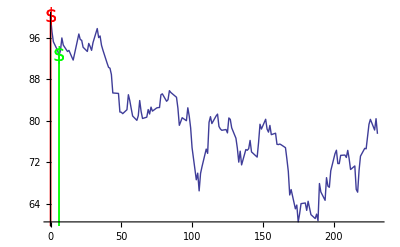

```mathematica
curParms=Prepend[Riffle[Internal`StringToDouble/@{"9.685327e+04","6.453123e-31","2.490016e-06","1.667109e+28","-2.302510e+00","-6.764583e-15",}[[;;-2]],{48,-26,-7,12,76,29,}[[;;-2]]],Internal`StringToDouble["4.115424e+06"]];
AbsoluteTiming[fitness[tickersData,mutatedParms=curParms]]
AbsoluteTiming[clFitnessEx[]]
stats=fitnessStats[tickersData[[1]],mutatedParms];
AbsoluteTiming[stats]
Show[ListPlot[tickersData[[1,All,{8,7}]],Joined->True],ListPlot[stats[[2,2]],Filling->Bottom,FillingStyle->Red,PlotMarkers->{"$",20},PlotStyle->Red],
ListPlot[stats[[3,2]],Filling->Bottom,FillingStyle->Green,PlotMarkers->{"$",20},PlotStyle->Green]
]
```

```mathematica
Print[StringForm["Current Fitness: ``\nCurrent Parameters: ``\n\nMutation Rounds: ``\nMutating Fitness: ``\nMutating Parameters: ``",Dynamic[curFitness],Dynamic[Column[curParms,Dividers->All,FrameStyle->Dotted,Alignment->Center,ItemSize->{16,2}]],Dynamic[rounds],Dynamic[mutatedFitness],Dynamic[Column[mutatedParms,Dividers->All,FrameStyle->Dotted,Alignment->Center,ItemSize->{16,2}]]
]];
SeedRandom[];
main[tickersData];
(*clMain[0];*)
```